```mathematica
ClearAll["Global`*"];
Galerkin[Np_,ϕ1_,ϕ2_,M_,Pr_,Ra_,β1_,β2_,Tw_,β_]:=Block[{e,u,θ,x,nodes,Bc1,Bc2,Bc3,Bc4,Bc5,Bc6,Bc7,R1,R2,Res1,Res2,sys,guess1,guess2,guess,sol1,B1,B2,Bifurcation,Criticalp,ρf,ρ1,ρ2,cpf,cp1,cp2,k1,k2,kf,σf,σ1,σ2,σnf,knf,A1,A2,A3,A4,A5},

ρ1=3970;ρ2=8933;ρf=997.1;cp1=765;cp2=385;cpf=4179;k1=40;k2=400;kf=0.613;
σ1=3.69*10^7;σ2=5.96*10^7;σf=0.05;

σnf=(σ1+2σf-2ϕ1(σf-σ1))/(σ1+2σf+ϕ1(σf-σ1))*σf;knf=(k1+2kf-2ϕ1(kf-k1))/(k1+2kf+ϕ1(kf-k1))*kf;
A1=1/((1-ϕ1)^2.5*(1-ϕ2)^2.5);
A2=(1-ϕ2)((1-ϕ1)+ϕ1*ρ1/ρf)+ϕ2*ρ2/ρf;
A3=(σ2+2σnf-2ϕ2(σnf-σ2))/(σ2+2σnf+ϕ2(σnf-σ2))*(σ1+2σf-2ϕ1(σf-σ1))/(σ1+2σf+ϕ1(σf-σ1));
A4=(k2+2knf-2ϕ2(knf-k2))/(k2+2knf+ϕ2(knf-k2))*(k1+2kf-2ϕ1(kf-k1))/(k1+2kf+ϕ1(kf-k1));
A5=(1-ϕ2)((1-ϕ1)+ϕ1*(ρ1*cp1)/(ρf*cpf))+ϕ2*(ρ2*cp2)/(ρf*cpf);

u=x (2-2 x^2+x^3)+(e (-1+x)^2 x (1+2 x))/(6*A1)+∑_(k=0)^Np a[k]*ChebyshevT[k, 2 x-1];
θ=∑_(k=0)^Np b[k]*ChebyshevT[k, 2 x-1];
nodes=N[Table[(1/2*(1-Cos[(i*π)/Np])),{i,0,Np}]];
Bc1=(u/.x->0)==0;
Bc2=(D[u, x,x]/.x->0)==0;
Bc3=(u/.x->1)==1;
Bc4=(D[u, x]/.x->1)==0;
Bc5=(A1*D[u, x,x]/.x->1)==e;
Bc6=((A4*D[θ, x]-β1*(θ-1))/.x->0)==0;
Bc7=((A4*D[θ, x]+β2*θ)/.x->1)==0;
R1=A1*D[u, {x,4}]-A2*Rey(D[u, {x,2}]*D[u, {x,1}]-u*D[u, {x,3}]+x*D[u, {x,3}]+3*D[u, {x,2}])-A3*M*D[u, {x,2}]-A1*β*D[u, {x,2}];
R2=A4*D[θ, {x,2}]-A5*Pr*Rey(x*D[θ, {x,1}]-u*D[θ, {x,1}])+Ra*D[((1+(Tw-1)θ)^3 D[θ, {x,1}]), x];
B1=Thread[(Table[R1/.x->nodes[[i]],{i,3,Np-1}])==0];
B2=Thread[(Table[R2/.x->nodes[[i]],{i,2,Np}])==0];
sys=Join[{Bc1,Bc2,Bc3,Bc4,Bc5,Bc6,Bc7,B1,B2}];

u0=x (2-2 x^2+x^3)+(e (-1+x)^2 x (1+2 x))/(6*A1);
Reyeqn=(A1*D[u0, {x,4}]-A2*Rey(D[u0, {x,2}]*D[u0, {x,1}]-u0*D[u0, {x,3}]+x*D[u0, {x,3}]+3*D[u0, {x,2}])-A3*M*D[u0, {x,2}]-A1*β*D[u0, {x,2}]/.x->0.1)==0;
Reyeqnsolve=Solve[Reyeqn,Rey]//Quiet;
Reyguess=Re[Rey/.Reyeqnsolve[[1]]];



guess1=Join[Table[{a[i],0},{i,0,Np}],{{Rey,Reyguess}}];
guess2=Table[{b[i],0},{i,0,Np}];
guess=Join[guess1,guess2];
sol1=Table[{e,Rey/.FindRoot[sys,guess,Method->{"Newton", "StepControl" -> "TrustRegion"},MaxIterations->100000]},{e,0,40,0.5}]

]
sol2=Galerkin[Np=30,ϕ1=0.1,ϕ2=0.04,M=1,Pr=6.2,Ra=0.5,β1=1,β2=1,Tw=1.2,β=0.1];
```

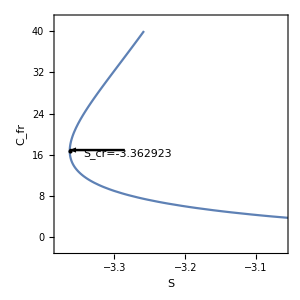

{-3.36292,{x→16.763}}

```mathematica
BB=Interpolation[sol2,InterpolationOrder->Np][x];
Criticalp=FindMinimum[BB,x]//Quiet;
Bifurcation=ParametricPlot[{BB,x},{x,0,40},Frame->True,Axes->{False,False},FrameLabel->{Style["S",Bold, 17],Style["C_fr",Bold,17]} ,AspectRatio->1,ImageSize->{300,300},Epilog->{PointSize[Large],Black,Point[{-3.3629227155882537,16.762978234828445}]}]//Quiet;
Print[Bifurcation];
Print[Criticalp];
```